# PDE as ODE?

## Definitions

Our frame of reference is set by the oldest individual in the sample. The year that individual was born is time zero. The constants τ, T, and A are all measured in the frame of reference. In contrast, the age variable a, is an individuals age.

τ	The time at which λ begins to change
a 	Age (this is the time variable)
T	The age of the oldest individual in the sample at the time of sampling
A 	The age of the focal individual at the time of sampling
λ0	The ancestral value of λ
α	The linear rate of change in λ

## Before the environment changes

Prior to the change in the environment, the probability that an individual is seronegative is given by the solution to:

```mathematica
OldstersBC=DSolve[{s'[a]==-(λ0)s[a],s[0]==1},s[a],a]
```

{{s[a]→ⅇ^(-a λ0)}}

This applies for T-A < τ and a < τ - (T-A)

## After the environment changes

### For individuals born before time τ

These individuals experience a change in λ at a = τ - (T-A)

After world starts to change at time τ, the probability that an individual is seronegative is given by the solution to:

```mathematica
OldstersAC=FullSimplify[DSolve[{s'[a]==-(λ0+α (T-A-τ+a))s[a],s[τ-(T-A)]==ⅇ^(-(τ-(T-A)) λ0)},s[a],a],Assumptions->{a>τ}]
```

{{s[a]→ⅇ^(-(a^2 α)/2-a λ0+a α (A-T+τ)-1/2 α (A-T+τ)^2)}}

```mathematica
FullSimplify[OldstersAC/.a->A]
```

{{s[A]→ⅇ^(-A λ0-1/2 α (T-τ)^2)}}

### For individuals born after time τ

```mathematica
Youngsters=FullSimplify[DSolve[{s'[a]==-(λ0+α (T-A-τ+a))s[a],s[0]==1},s[a],a],Assumptions->{a>τ}]
```

{{s[a]→ⅇ^(-1/2 a (a α+2 λ0-2 α (A-T+τ)))}}

```mathematica
FullSimplify[Youngsters/.a->A]
```

{{s[A]→ⅇ^(1/2 A (-2 λ0+α (A-2 T+2 τ)))}}

## Plot solutions and check

### First, plot an individual born after the change

```mathematica
Parms={λ0->.01,α->.001,τ->50,A->10,T->80};
```

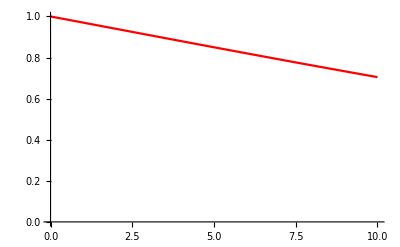

```mathematica
YoungPlot=Plot[{s[a]/.Youngsters/.Parms},{a,0,A/.Parms},PlotRange->{{0,A/.Parms},{0,1}},PlotStyle->Red]
```

This seems to check out...

### Second, plot an individual born before the change

```mathematica
Parms={λ0->.01,α->.001,τ->40,A->70,T->80};
```

For the parameters you selected the individual experienced the change in the environment at age:

```mathematica
(τ-(T-A))/.Parms
```

30

If this is not a positive number you need to select new parameters as your individual was born after the change and you should be using the solution in the previous section

#### First, plot their early life (Do you even need this for the MLE? I do not think so because we are conditioned on a=A)

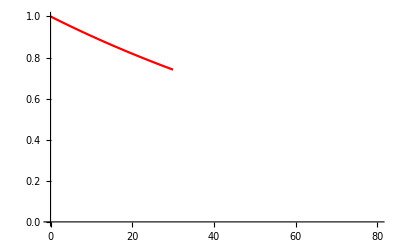

```mathematica
EarlyPlot=Plot[{s[a]/.OldstersBC/.Parms},{a,0,(τ-(T-A))/.Parms},PlotRange->{{0,T/.Parms},{0,1}},PlotStyle->Red]
```

#### Then their late life

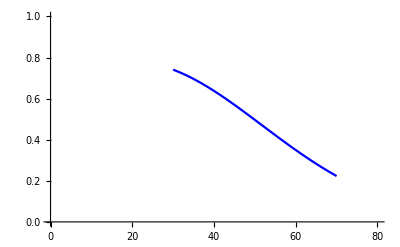

```mathematica
LatePlot=Plot[{s[a]/.OldstersAC/.Parms},{a,(τ-(T-A))/.Parms,A/.Parms},PlotRange->{{0,T/.Parms},{0,1}},PlotStyle->Blue]
```

#### And combine into their full life

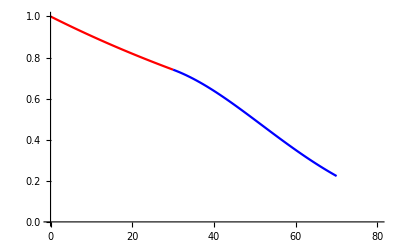

```mathematica
Show[{EarlyPlot,LatePlot}]
```

## Plot and Simulate Data for a Sample

```mathematica
Pars={τ->70,T->80,λ0->.01,α->.005};
```

Here, i plays the role of current A of individuals

```mathematica
Module[{i,j},ToPlot={};For[i=0,i<=T/.Pars,i++,If[i<=((T-τ)/.Pars),PN=((s[a]/.Youngsters/.a->i/.A->i/.Pars))];If[i>((T-τ)/.Pars),PN=((s[a]/.OldstersAC/.a->i/.A->i/.Pars))];ToPlot=Append[ToPlot,{i,PN[[1]]}]]]
```

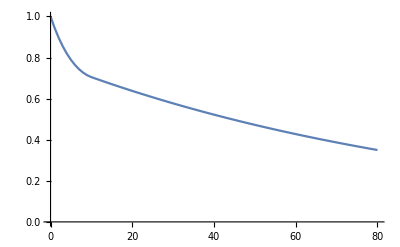

```mathematica
ListPlot[ToPlot,Joined->True,PlotRange->{0,1}]
```

## ML Estimation

Note that here you will set the parameters A and T based on the sample. The parameters λ0, τ, and α will be estimated. The Likelihood function will be piecewise and will need to access one of the three solutions above depending on the individuals age and the value of τ. Its a bit clunky but it should be very fast.